Multi Dimensional scaling - symmetric data dimensional reduction technique

```mathematica
candybars={"Snickers","Hershey’s","Kit Kat","Twix","3 Musketeers"," Milky Way Bar"}
Subsets[candybars,{2}]//Grid
```

{Snickers,Hershey’s,Kit Kat,Twix,3 Musketeers, Milky Way Bar}

Snickers | Hershey’s
Snickers | Kit Kat
Snickers | Twix
Snickers | 3 Musketeers
Snickers |  Milky Way Bar
Hershey’s | Kit Kat
Hershey’s | Twix
Hershey’s | 3 Musketeers
Hershey’s |  Milky Way Bar
Kit Kat | Twix
Kit Kat | 3 Musketeers
Kit Kat |  Milky Way Bar
Twix | 3 Musketeers
Twix |  Milky Way Bar
3 Musketeers |  Milky Way Bar

```mathematica
(*  6 candy bar each pair rank from 1-15 on how similar they are*)
candybardata={{0, □, □, □, □, □}, {□, 0, □, □, □, □}, {□, □, 0, □, □, □}, {□, □, □, 0, □, □}, {□, □, □, □, 0, □}, {□, □, □, □, □, 0}}
```

{{0,2,13,4,3,8},{2,0,12,6,5,7},{13,12,0,9,10,11},{4,6,9,0,1,14},{3,5,10,1,0,15},{8,7,11,14,15,0}}

```mathematica
cbparams=genrules[6]
```

{x[1]→{0,0},x[2]→{0,0},x[3]→{0,0},x[4]→{0,0},x[5]→{0,0},x[6]→{0,0}}

```mathematica
n=6;
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+candybardata[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,6},{j,2}]]]
```

(2-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2))^2+(13-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2))^2+(12-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2))^2+(4-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2))^2+(6-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2))^2+(9-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2))^2+(3-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2))^2+(5-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2))^2+(10-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2))^2+(1-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2))^2+(8-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2))^2+(7-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2))^2+(11-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2))^2+(14-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2))^2+(15-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2))^2

{15.7821,{x[1,1]→-0.615405,x[1,2]→-2.46336,x[2,1]→-2.37795,x[2,2]→-1.67518,x[3,1]→2.06942,x[3,2]→8.79786,x[4,1]→3.76744,x[4,2]→-0.819197,x[5,1]→3.39506,x[5,2]→-1.90946,x[6,1]→-8.48426,x[6,2]→3.28646}}

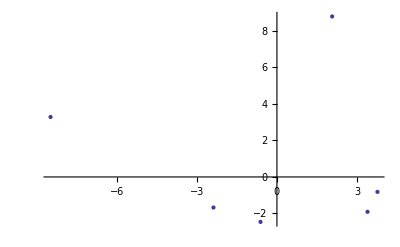

```mathematica
Partition[mds[[2,All,-1]],2] // ListPlot
```

```mathematica
drivetime[{city1_String,city2_String}]:=Module[{test},
test=Import["https://maps.googleapis.com/maps/api/directions/json?origin="<>city1<>"&destination="<>city2<>"&sensor=false","JSON"];
Cases[test,HoldPattern["duration"->value_]:>value,Infinity][[1,2,2]]]
cities={"New_York","Los_Angeles","Chicago","Houston","Philadelphia","Phoenix","San_Antonio","San_Diego","Dallas","San_Jose"};
pairs=Tuples[cities,2]
times=drivetime /@ pairs
matrix=Partition[times,10]
```

{{New_York,New_York},{New_York,Los_Angeles},{New_York,Chicago},{New_York,Houston},{New_York,Philadelphia},{New_York,Phoenix},{New_York,San_Antonio},{New_York,San_Diego},{New_York,Dallas},{New_York,San_Jose},{Los_Angeles,New_York},{Los_Angeles,Los_Angeles},{Los_Angeles,Chicago},{Los_Angeles,Houston},{Los_Angeles,Philadelphia},{Los_Angeles,Phoenix},{Los_Angeles,San_Antonio},{Los_Angeles,San_Diego},{Los_Angeles,Dallas},{Los_Angeles,San_Jose},{Chicago,New_York},{Chicago,Los_Angeles},{Chicago,Chicago},{Chicago,Houston},{Chicago,Philadelphia},{Chicago,Phoenix},{Chicago,San_Antonio},{Chicago,San_Diego},{Chicago,Dallas},{Chicago,San_Jose},{Houston,New_York},{Houston,Los_Angeles},{Houston,Chicago},{Houston,Houston},{Houston,Philadelphia},{Houston,Phoenix},{Houston,San_Antonio},{Houston,San_Diego},{Houston,Dallas},{Houston,San_Jose},{Philadelphia,New_York},{Philadelphia,Los_Angeles},{Philadelphia,Chicago},{Philadelphia,Houston},{Philadelphia,Philadelphia},{Philadelphia,Phoenix},{Philadelphia,San_Antonio},{Philadelphia,San_Diego},{Philadelphia,Dallas},{Philadelphia,San_Jose},{Phoenix,New_York},{Phoenix,Los_Angeles},{Phoenix,Chicago},{Phoenix,Houston},{Phoenix,Philadelphia},{Phoenix,Phoenix},{Phoenix,San_Antonio},{Phoenix,San_Diego},{Phoenix,Dallas},{Phoenix,San_Jose},{San_Antonio,New_York},{San_Antonio,Los_Angeles},{San_Antonio,Chicago},{San_Antonio,Houston},{San_Antonio,Philadelphia},{San_Antonio,Phoenix},{San_Antonio,San_Antonio},{San_Antonio,San_Diego},{San_Antonio,Dallas},{San_Antonio,San_Jose},{San_Diego,New_York},{San_Diego,Los_Angeles},{San_Diego,Chicago},{San_Diego,Houston},{San_Diego,Philadelphia},{San_Diego,Phoenix},{San_Diego,San_Antonio},{San_Diego,San_Diego},{San_Diego,Dallas},{San_Diego,San_Jose},{Dallas,New_York},{Dallas,Los_Angeles},{Dallas,Chicago},{Dallas,Houston},{Dallas,Philadelphia},{Dallas,Phoenix},{Dallas,San_Antonio},{Dallas,San_Diego},{Dallas,Dallas},{Dallas,San_Jose},{San_Jose,New_York},{San_Jose,Los_Angeles},{San_Jose,Chicago},{San_Jose,Houston},{San_Jose,Philadelphia},{San_Jose,Phoenix},{San_Jose,San_Antonio},{San_Jose,San_Diego},{San_Jose,Dallas},{San_Jose,San_Jose}}

{0,145170,42863,85220,6041,128442,95250,146463,81566,154382,145259,0,103670,77929,141914,19253,68024,7045,72881,18056,43082,103458,0,58920,41163,92667,65358,106630,50632,112670,85342,77632,58787,0,81297,58720,10213,73201,12403,95123,6017,142271,41068,81111,0,124691,91141,142712,77457,152586,128338,19175,92337,58989,124359,0,49084,18377,53941,36666,95407,67865,65228,10239,91362,48953,0,63434,14906,85356,146247,7136,106843,73364,142268,18345,63459,0,68316,24986,81673,72690,50522,12376,77628,53778,14832,68259,0,88539,153760,18081,112171,95507,151841,36831,85602,25044,87787,0}

{{0,145170,42863,85220,6041,128442,95250,146463,81566,154382},{145259,0,103670,77929,141914,19253,68024,7045,72881,18056},{43082,103458,0,58920,41163,92667,65358,106630,50632,112670},{85342,77632,58787,0,81297,58720,10213,73201,12403,95123},{6017,142271,41068,81111,0,124691,91141,142712,77457,152586},{128338,19175,92337,58989,124359,0,49084,18377,53941,36666},{95407,67865,65228,10239,91362,48953,0,63434,14906,85356},{146247,7136,106843,73364,142268,18345,63459,0,68316,24986},{81673,72690,50522,12376,77628,53778,14832,68259,0,88539},{153760,18081,112171,95507,151841,36831,85602,25044,87787,0}}

{Point[{-59529.4,-62803.4}],Point[{51461.,30588.4}],Point[{-21802.4,-43883.9}],Point[{-24827.4,15590.5}],Point[{-60389.2,-57129.5}],Point[{32227.1,28263.8}],Point[{-15976.8,21692.2}],Point[{46643.2,36758.2}],Point[{-16765.6,6678.34}],Point[{68906.9,24098.3}]}

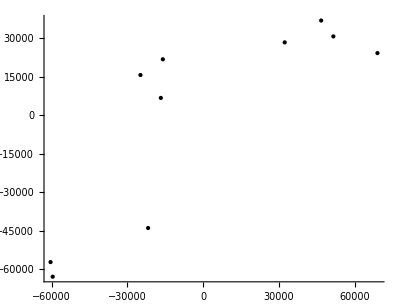

```mathematica
mudisc[mat_,dims_]:=Module[{leng,x,stress,temp},
leng=mat //Length;
stress=Sum[(Norm[Table[x[i,k],{k,dims}]-Table[x[j,k],{k,dims}]]-mat[[i,j]])^2,{i,leng},{j,i,leng}];
temp=NMinimize[stress,Table[x[i,k],{i,leng},{k,dims}]//Flatten];
Partition[temp[[2,All,-1]],2]
]
grp=Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{cities,mudisc[matrix,2]}]
Graphics[grp, Axes->True]
```